```mathematica
l = Reverse[IntegerDigits[Range[0,7],2,3]]
```

{{1,1,1},{1,1,0},{1,0,1},{1,0,0},{0,1,1},{0,1,0},{0,0,1},{0,0,0}}

```mathematica
row = RandomInteger[1,20]
```

{0,1,0,1,0,1,0,1,1,0,1,0,0,1,1,1,1,1,1,0}

```mathematica
Partition[row,3,1,2]
```

{{0,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,1},{0,1,0},{1,0,1},{0,1,1},{1,1,0},{1,0,1},{0,1,0},{1,0,0},{0,0,1},{0,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,0},{1,0,0}}

```mathematica
r1 = MapThread[Rule,{l,IntegerDigits[30,2,8]}]
```

{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

```mathematica
Partition[row,3,1]/.r1
```

{1,0,1,0,1,0,1,0,0,1,1,1,1,0,0,0,0,0}

```mathematica
CAStep[rls_,row_] := Partition[row,3,1,2]/.rls
```

```mathematica
CAEvolve[rlnum_Integer,init_,steps_] := Module[
{rls},rls=MapThread[Rule,{Reverse[IntegerDigits[#,2,3]&/@Range[0,7]],IntegerDigits
[rlnum,2,8]}];
NestList[CAStep[rls,#]&,init,steps]
]
```

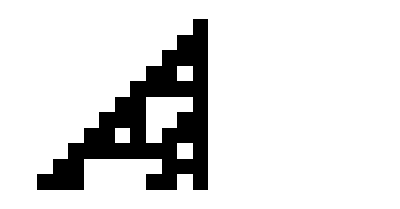

```mathematica
ArrayPlot[CAEvolve[110,ReplacePart[Table[0,{21}],11->1],10]]
```

```mathematica
DeleteCases[r1,HoldPattern[{1,1,1}->_]]
```

{{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

```mathematica
RandomReal[]
```

0.3796

```mathematica
{1,1,1}->If[RandomReal[]<p,{1,1,1}/.r1,1]
```